```mathematica
r=1;
Manipulate[
ParametricPlot[
{
r+(1/2-Abs[-1+Mod[t,2]])Cos[θ]-(1/2-Abs[-1+Mod[1/2+t,2]])Sin[θ],
(1/2-Abs[-1+Mod[1/2+t,2]])Cos[θ]+(1/2-Abs[-1+Mod[t,2]])Sin[θ]
},
{t,0,2},PerformanceGoal->"Quality"
],
{θ,0,π/2}
]
```

```mathematica
x[t_]:=Cos[nx t+θx];
y[t_]:=Cos[ny t+θy];
z[t_]:=Cos[nz t + θz];
nx=3 ;
ny=5 ;
nz=7;
θx=0;
θy=π/4;
θz=π/12;
ParametricPlot3D[{x[t],y[t],z[t]},{t,-π,π},PlotStyle->Tube[0.03]]
```

x+x^3/3+(2 x^5)/15

x+x^3/3+(2 x^5)/15+(17 x^7)/315+O[x]^8

x+x^3/3+(2 x^5)/15

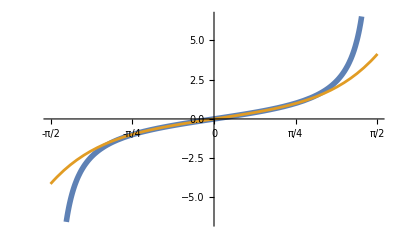

```mathematica
(* Series *)

(* finding the 5Th degree Taylor Polynomial for tan[x] near zero *)

tpoly=Sum[
(D[Tan[x],{x,n}]/.x->0)x^n/(n!),{n,0,5}
]
Series[Tan[x],{x,0,7}]
tbuiltin=Normal@Series[Tan[x],{x,0,5}]
Plot[{Tan[x],tpoly},{x,-π/2,π/2},
PlotStyle->{Thickness[0.01],Thickness[0.005]},
Ticks->{Table[k π/2,{k,-1,1,1/2}],Automatic}
]
```

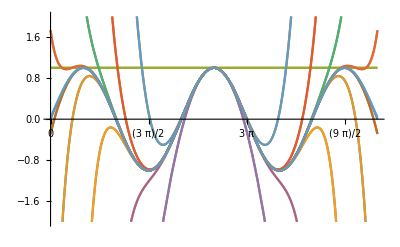

```mathematica
(* taylor series for sin[x] near 5 π/2 *)
spoly=Table[
Normal@Series[Sin[x],{x,5 π/2,k}],
{k,0,20}
];
Plot[{Sin[x],spoly},{x,0,5π},
Ticks->{Table[k π/2,{k,0,10}],Automatic},
PlotRange->{{0,5π},{-2,2}}
]
```